```mathematica
Clear["Global`*"]
```

```mathematica
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={0,R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{0,a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)},{0,a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{0,a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{0,a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{0,a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Direction solution of the Bellman equation*)
V=Inverse[IdentityMatrix[5] - gamma*Pmat].Rmat;
```

```mathematica
(*Series expansion of the solution*)
Series[V,{gamma,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+a0 S-a0 b0 S+b0 T-a0 b0 T) gamma+O[gamma]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+a1 S-a1 b1 S+b1 T-a1 b1 T) gamma+O[gamma]^2,S+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+a2 S-a2 b2 S+b2 T-a2 b2 T) gamma+O[gamma]^2,T+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+a3 S-a3 b3 S+b3 T-a3 b3 T) gamma+O[gamma]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+a4 S-a4 b4 S+b4 T-a4 b4 T) gamma+O[gamma]^2}

```mathematica
(*dV1/da_0(gamma) -------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*Initial: random, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=1;b3=0;b4=0;
Va0 = D[V,a0]
FindRoot[Va0[[1]],{gamma,0.5}]
```

{(3 (gamma-0.5 gamma^2-0.5 gamma^3))/(1.-1. gamma)+(5 (-gamma+1.5 gamma^2-0.5 gamma^3))/(1.-1. gamma)+(-0.5 gamma^2+0.5 gamma^3)/(1.-1. gamma),0,0,0,0}

{gamma→0.571429}

{(3 (gamma-gamma^2))/(1-2 gamma+gamma^2)+(5 (-gamma+2 gamma^2-gamma^3))/(1-2 gamma+gamma^2),0,0,0,0}

{gamma→0.4}

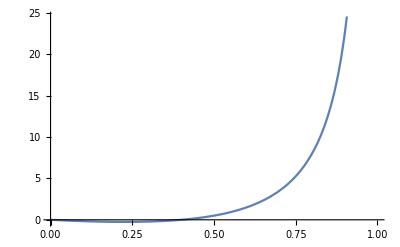

```mathematica
(*Initial: all-coop; versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0]
FindRoot[Va0[[1]],{gamma,0.5}]
Plot[Va0[[1]],{gamma,0,1}]
```

{(3 (gamma-0.5 gamma^2-0.5 gamma^3))/(1.-1. gamma)+(5 (-gamma+1.5 gamma^2-0.5 gamma^3))/(1.-1. gamma)+(-0.5 gamma^2+0.5 gamma^3)/(1.-1. gamma),0,0,0,0}

{gamma→0.571429}

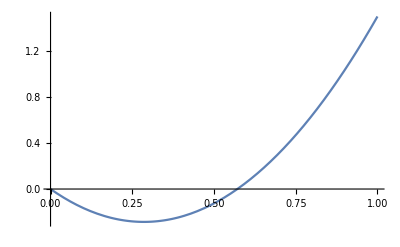

```mathematica
(*Initial: random, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0]
FindRoot[Va0[[1]],{gamma,0.5}]
Plot[Va0[[1]],{gamma,0,1}]
```

{(5 (-gamma+gamma^2))/(1-gamma^2)+(3 (gamma-gamma^3))/(1-gamma^2)+(-gamma^2+gamma^3)/(1-gamma^2),0,0,0,0}

{gamma→1.}

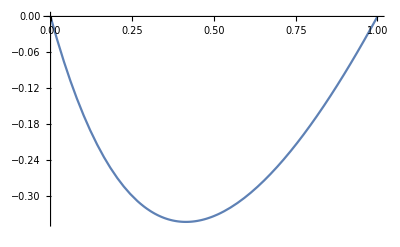

```mathematica
(*Initial: all-defect, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=0;b3=0;b4=1;
Va0 = D[V,a0]
FindRoot[Va0[[1]],{gamma,0.5}]
Plot[Va0[[1]],{gamma,0,1}]
```

```mathematica
(*Vj(a_i) for tit-for-tat ------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*Initial: all-coop, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a = 1
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=1/3;
(*gamma = 2/3;*)
(*gamma = 1/3;*)
Simplify[V]
```

1

{3/2,9/2,3/2,11/2,3/2}

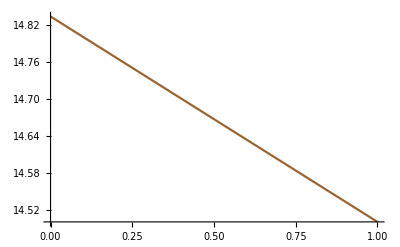

```mathematica
(*a0*)
Clear[a0]
a1=a;a2=a;a3=a;a4=a;
pltV1a0 = Plot[V[[1]],{a0,0,1},PlotStyle->Red];
pltV2a0 = Plot[V[[2]],{a0,0,1},PlotStyle->Green];
pltV3a0 = Plot[V[[3]],{a0,0,1},PlotStyle->Blue];
pltV4a0 = Plot[V[[4]],{a0,0,1},PlotStyle->Black];
pltV5a0 = Plot[V[[5]],{a0,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a0,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

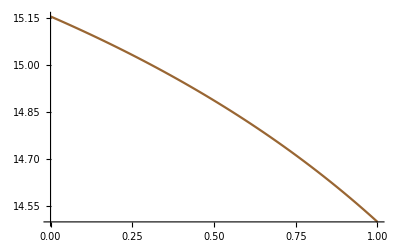

```mathematica
(*a1*)
Clear[a1]
a0=a;a2=a;a3=a;a4=a;
pltV1a1 = Plot[V[[1]],{a1,0,1},PlotStyle->Red];
pltV2a1 = Plot[V[[2]],{a1,0,1},PlotStyle->Green];
pltV3a1 = Plot[V[[3]],{a1,0,1},PlotStyle->Blue];
pltV4a1 = Plot[V[[4]],{a1,0,1},PlotStyle->Black];
pltV5a1 = Plot[V[[5]],{a1,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a1,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

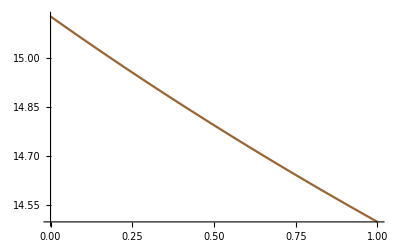

```mathematica
(*a2*)
Clear[a2]
a0=a;a1=a;a3=a;a4=a;
pltV1a2 = Plot[V[[1]],{a2,0,1},PlotStyle->Red];
pltV2a2 = Plot[V[[2]],{a2,0,1},PlotStyle->Green];
pltV3a2 = Plot[V[[3]],{a2,0,1},PlotStyle->Blue];
pltV4a2 = Plot[V[[4]],{a2,0,1},PlotStyle->Black];
pltV5a2 = Plot[V[[5]],{a2,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a2,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

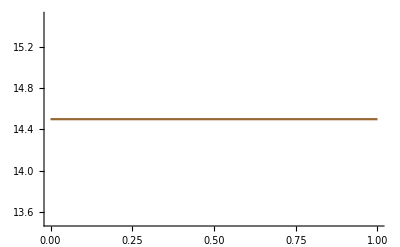

```mathematica
(*a3*)
Clear[a3]
(*a0=0.7;a1=0.38;a2=0.48;a4=0.994;*)
a0=a;a1=a;a2=a;a4=a;
pltV1a3 = Plot[V[[1]],{a3,0,1},PlotStyle->Red];
pltV2a3 = Plot[V[[2]],{a3,0,1},PlotStyle->Green];
pltV3a3 = Plot[V[[3]],{a3,0,1},PlotStyle->Blue];
pltV4a3 = Plot[V[[4]],{a3,0,1},PlotStyle->Black];
pltV5a3 = Plot[V[[5]],{a3,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a3,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

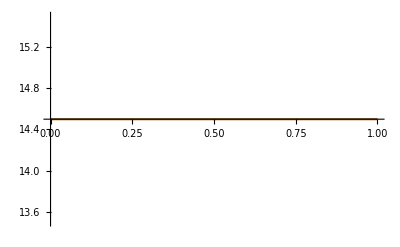

```mathematica
(*a3*)
Clear[a4]
a0=a;a1=a;a2=a;a3=a;
pltV1a4 = Plot[V[[1]],{a4,0,1},PlotStyle->Red];
pltV2a4 = Plot[V[[2]],{a4,0,1},PlotStyle->Green];
pltV3a4 = Plot[V[[3]],{a4,0,1},PlotStyle->Blue];
pltV4a4 = Plot[V[[4]],{a4,0,1},PlotStyle->Black];
pltV5a4 = Plot[V[[5]],{a4,0,1},PlotStyle->Yellow];
pltVsum = Plot[Total[V],{a4,0,1},PlotStyle->Brown];
Show[pltVsum,PlotRange->All]
```

```mathematica
(*V1(a0) ---------------------------------------------------------------------------------------------------------------------------------------*)
```

4/7

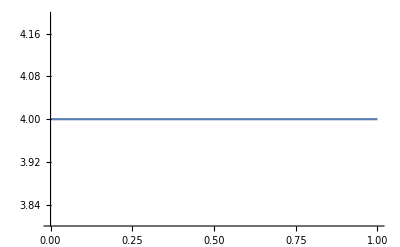

{4.+4.44089×10^-16 a0,7.,4.,7.,3.}

```mathematica
(*Initial: random, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=4/7
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

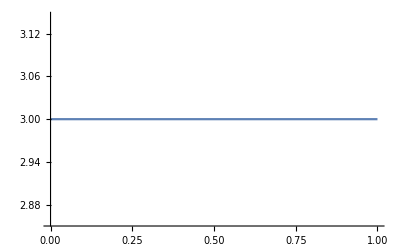

{3,6,3,6,2}

```mathematica
(*Initial: all-defect, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=1/2;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

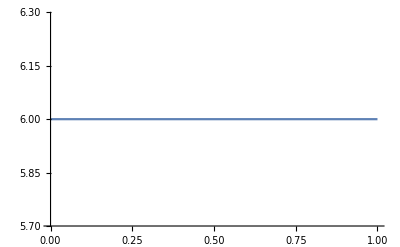

{6,9,6,9,5}

```mathematica
(*Initial: all-coop, versus Tit-for-Tat*)
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=1;b3=0;b4=0;
gamma=2/3;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

```mathematica
(*Initial: random, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0.5;a2=0.5;a3=0.5;a4=0.5;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=4/7;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

-Graphics-

{4.-1.33227×10^-15 a0,7.,2.,7.,5.}

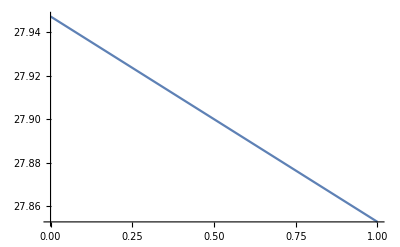

{27.9474-0.0947368 a0,30.9474,26.0526,31.0526,28.9474}

```mathematica
(*Initial: all-defect, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=0;a2=0;a3=0;a4=0;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=0.9;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```

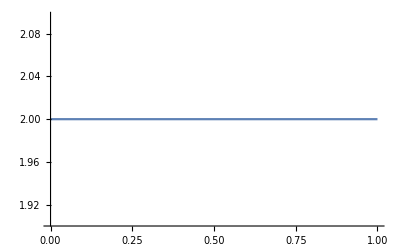

{2,5,0,5,3}

```mathematica
(*Initial: all-coop, versus win-stay-lose-shift (Pavlov)*)
R=3;S=0;T=5;P=1;
a1=1;a2=1;a3=1;a4=1;
b0=1; b1=1;b2=0;b3=0;b4=1;
gamma=2/5;
Plot[V[[1]],{a0,0,1}]
Simplify[V]
```